```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
journalStyle={FontSize->10 (* acm default font for text *)};
```

### BKT model functional form

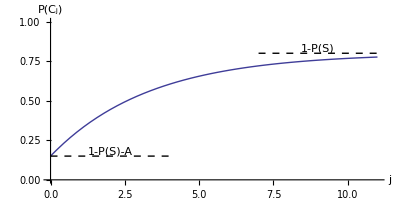

```mathematica
bktPlot=Block[{b=0.3,pg=.15,ps=0.2,nn=11},Plot[1-ps-(1-pg-ps)  Exp[-b x],{x,0,nn},PlotRange->{0,1},AxesLabel->{"j",SequenceForm["P(",Subscript["C","j"],")"]},BaseStyle->journalStyle, AspectRatio->1/2,Epilog->{Text["1-P(S)-A",{2,pg},{0,-1}],Text["1-P(S)",{nn-2,1-ps},{0,-1}],Dashed,Line[{{0,pg},{4,pg}}],Line[{{nn-4,1-ps},{nn,1-ps}}]}]]
```

```mathematica
Export["exponential.eps",bktPlot]
```

exponential.eps

Values for A to match Table 1 in Beck and Chang paper.

```mathematica
(1-ps-pg)(1-p0)/.{ps->0.05,pg->0.3,p0->0.36}
```

0.416

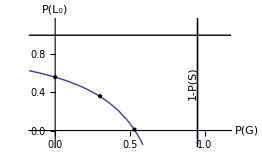

```mathematica
table1=Block[{aa=.418,ps=0.05,bd=0.15},Plot[1-aa/(1-pg-ps),{pg,-1,1},PlotRange->{{-bd,1+bd},{-bd,1+bd}},AxesLabel->{"P(G)",SequenceForm["P(",Subscript["L","0"],")"]},BaseStyle->journalStyle, Epilog->{Text["1-P(S)",{1-ps,1/2},{0,-1},{0,1}],Line[{{1-ps,-1},{1-ps,2}}],Line[{{-1,1},{2,1}}],PointSize[Medium],Point[{.3,.36}],Point[{0,.56}],Point[{0.53,0.01}]}]]
```

```mathematica
Export["table1.eps",table1]
```

table1.eps

### BKT model recursion

Values from Table 1, "Guess model" of Beck and Chang paper.

```mathematica
vals={ps->0.05, pg->0.3, pl->0.1, p0->0.36};
```

```mathematica
recursion["correct",plast_]:=1-(1-pl)(1-plast) pg/(pg+(1-ps-pg) plast);
recursion["incorrect",plast_]:=1-(1-pl)(1-plast)(1-pg)/(1-pg-(1-ps-pg) plast);
```

Find fixed points of the recursion

```mathematica
fcorrect=Solve[recursion["correct",plast]==plast,plast]
```

{{plast→1},{plast→(pg pl)/(-1+pg+ps)}}

```mathematica
fcorrect/.vals
```

{{plast→1},{plast→-0.0461538}}

```mathematica
fincorrect=Solve[recursion["incorrect",plast]==plast,plast]
```

{{plast→1},{plast→(-pl+pg pl)/(-1+pg+ps)}}

Expansion about fixed points

```mathematica
Simplify[Series[recursion["correct",plast],{plast,1,1}]]
```

1+(pg (-1+pl) (plast-1))/(-1+ps)+O[plast-1]^2

```mathematica
Simplify[Series[recursion["incorrect",plast],{plast,(1-pg) pt/(1-pg-ps),1}]]
```

(ps pt-pl (-1+pg+ps+pt-pg pt))/((-1+pg+ps) (-1+pt))+((-1+pl) ps (plast-((-1+pg) pt)/(-1+pg+ps)))/((-1+pg) (-1+pt)^2)+O[plast-((-1+pg) pt)/(-1+pg+ps)]^2

If we confine our attention to the region 0<P_j<1, the “j correct” recursion relation has a stable fixed point at 1.  Near that point, convergence is exponentially fast.  Similarly, the “j incorrect” recursion relation has a stable fixed point at (1-P(G)) P(T)/(1-P(G)-P(S)).  Near that point, convergence is also exponentially fast.

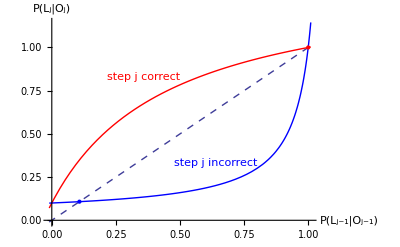

```mathematica
pRecursion=Plot[{plast,recursion["correct",plast]/.vals,recursion["incorrect",plast]/.vals},{plast,-0.01,1.01},Epilog->{PointSize[Large],{Red,Point[{1,1}],Text["step j correct",{0.5,.8},{1,-1}]},{Blue,Point[{1,1} plast/.fincorrect[[2]]/.vals],Text["step j incorrect",{0.8,.3},{1,-1}]}},PlotStyle->{Dashed,Red,Blue},AxesLabel->{SequenceForm["P(",Subscript["L","j-1"],"|",Subscript["O","j-1"],")"],SequenceForm["P(",Subscript["L","j"],"|",Subscript["O","j"],")"]},BaseStyle->journalStyle]
```

```mathematica
Export["p-recursion.eps",pRecursion]
```

p-recursion.eps

The demand that the incorrect step fixed point be less than 1 provides the strongest constraint on model parameters.

```mathematica
Plot3D[1-ps/(1-pg),{pg,0,1},{ps,0,1},PlotRange->{0,1},AxesLabel->{"P(G)","P(S)","P(T)"},ClippingStyle->None]
```

-Graphics3D-

See how things change as one moves from positive to negative learning parameters.  We see that “Correct” and “incorrect” invert roles.

```mathematica
Map[Function[vals,Plot[{plast,recursion["correct",plast]/.vals,recursion["incorrect",plast]/.vals},{plast,-0.01,1.01},Epilog->{PointSize[Large],{Red,Point[{1,1}],Text["step j correct",{0.5,.8},{1,-1}]},{Blue,Point[{1,1} plast/.fincorrect[[2]]/.vals],Text["step j incorrect",{0.8,.3},{1,-1}]}},PlotStyle->{Dashed,Red,Blue},AxesLabel->{SequenceForm["P(",Subscript["L","j-1"],")"],SequenceForm["P(",Subscript["L","j"],")"]},BaseStyle->{FontSize->12}]],{{ps->0.2, pg->0.2, pl->0.2, p0->0.36},{ps->0.4, pg->0.4, pl->0.2, p0->0.36},{ps->0.6, pg->0.6, pl->0.2, p0->0.36},{ps->0.8, pg->0.8, pl->0.2, p0->0.36}}]
```